# My Solar Eclipse Viewing

The plot below shows the overall path of the April 2024 eclipse, as well as some additional information about the eclipse coverage in different areas (contour lines), and the earth’s first (P1 & P2) and last (P3 & P4) contact with the moon’s shadow. I have added a green marker to show where I was during the eclipse.

```mathematica
eclipseMap = SolarEclipse[DateObject[{2024, 4, 8}], "EclipseMap"];
me = GeoPosition[{34.1,-84.2}];
```

```mathematica
Show[eclipseMap, GeoGraphics[{GeoMarker[me, "Color"->Green]}]]
```

-Graphics-

At my location, the maximum coverage was about 83%, occurring at 3:05 local time.

```mathematica
SolarEclipse[DateObject[{2024, 4, 8}], {"LocalMaximumEclipseDate",me}]
SolarEclipse[DateObject[{2024, 4, 8}], {"LocalMaximumEclipseObscuration",me}]
```

Mon 8 Apr 2024 15:05:19GMT-4

0.826597

My viewing setup was a unique mix of basic and fancy: an old Calumet CC-400  view camera with a pinhole “lens” consisting of some aluminum foil punctured by a mechanical pencil.

```mathematica
Import[NotebookDirectory[]<>"PinholeCamera.jpg"]
```

-Graphics-

The camera itself is essentially just empty space - a place to hold the lens on the front, a place to hold film on the back, and a light-tight tube connecting the two. When the film is removed, the lens instead projects an image on a piece of ground glass, allowing you to compose a photo (as long as you’re in a dark enough space, which is why old photographers are often seen huddling under a cloth hood). The resultant image on the ground glass is upside-down, something handheld cameras correct with a pentaprism, and backwards, due to viewing the image “from behind” as it is projected on the ground glass. See the image below, taken by Cameron Shaw, as an example of these effects:

```mathematica
Import[NotebookDirectory[]<>"GroundGlass.jpg"]
```

-Graphics-

The result wasn’t the prettiest thing in the world, but it worked! At 3:10, I snapped the photo of the eclipse shown to the right below. Unsurprisingly, it matches perfectly with Mathematica’s visualization for my time and location (shown on the left)! It is easy to see the mirroring I mentioned earlier, and if you look closely enough, you can make out the inversion as well.

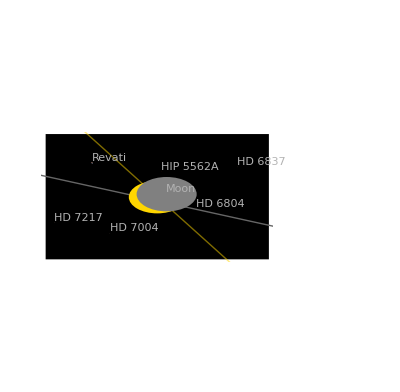

```mathematica
GraphicsRow[{
AstroGraphics[Entity["Star","Sun"],
AstroReferenceFrame->{me,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]},AstroRange->Quantity[1, "AngularDegrees"]],Import[NotebookDirectory[]<>"PinholeEclipse.jpg"]}]
```

I had some friends travel to Dallas, Texas and Rochester, New York to view the eclipse in totality. Rochester was cloudy, but its still cool to look at all three locations simultaneously to “watch” the eclipse transit the US!

```mathematica
tx =Entity["City",{"Dallas","Texas","UnitedStates"}];
ny = Entity["City",{"Rochester","NewYork","UnitedStates"}];
mtNebo = GeoPosition[{35.2,-93.2}];
friendMap = 
Show[eclipseMap,
GeoGraphics[{
GeoMarker[me,"Color"->Green, Scale->0.05], 
GeoMarker[tx, "Color" -> Green, Scale->0.05],
GeoMarker[ny, "Color" -> Green, Scale->0.05],
GeoMarker[mtNebo, "Color"->Green, Scale->0.05]
}]
]

Animate[
Column[{
Row[{Spacer[150],"The Eclipse From Different Cities"}],
Grid[{
{Text["Dallas, TX"],Text["Mt. Nebo, AR"],Text["Atlanta, GA"], Text["Rochester, NY"]},
{
AstroGraphics[Entity["Star","Sun"],AstroReferenceFrame->{tx,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]+n*Quantity[15, "Minutes"]},AstroRange->Quantity[1, "AngularDegrees"]],
AstroGraphics[Entity["Star","Sun"],AstroReferenceFrame->{mtNebo,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]+n*Quantity[15, "Minutes"]},AstroRange->Quantity[1, "AngularDegrees"]],
AstroGraphics[Entity["Star","Sun"],AstroReferenceFrame->{me,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]+n*Quantity[15, "Minutes"]},AstroRange->Quantity[1, "AngularDegrees"]],
AstroGraphics[Entity["Star","Sun"],AstroReferenceFrame->{ny,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]+n*Quantity[15, "Minutes"]},AstroRange->Quantity[1, "AngularDegrees"]]
},
{
Import[NotebookDirectory[]<>"TXEclipse.jpg"],
Import[NotebookDirectory[]<>"Nebo.jpeg"],
Import[NotebookDirectory[]<>"PinholeEclipse.jpg"],
Import[NotebookDirectory[]<>"NYEclipse.png"]
}
}]
}],  
{n, -5, 5}]
```

-Graphics-

```mathematica
gif =Table[
Grid[{
{Text["Dallas, TX"],Text["Atlanta, GA"], Text["Rochester, NY"]},
{
AstroGraphics[Entity["Star","Sun"],AstroReferenceFrame->{tx,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]+n*Quantity[15, "Minutes"]},AstroRange->Quantity[1, "AngularDegrees"]],
AstroGraphics[Entity["Star","Sun"],AstroReferenceFrame->{me,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]+n*Quantity[15, "Minutes"]},AstroRange->Quantity[1, "AngularDegrees"]],
AstroGraphics[Entity["Star","Sun"],AstroReferenceFrame->{ny,DateObject[{2024,4,8,15,10},"Minute","Gregorian",-4.]+n*Quantity[15, "Minutes"]},AstroRange->Quantity[1, "AngularDegrees"]]
},
{
Import["C:\\Users\\brent\\Documents\\GitHub\\MyEclipse_2024\\TXEclipse.jpg"],
Import["C:\\Users\\brent\\Documents\\GitHub\\MyEclipse_2024\\PinholeEclipse.jpg"],
Import["C:\\Users\\brent\\Documents\\GitHub\\MyEclipse_2024\\NYEclipse.png"]
}
}],  
{n, -5, 5, 0.2}];
Export["C:\\Users\\brent\\Documents\\GitHub\\MyEclipse_2024\\DifferentCities.gif", gif]
Export["C:\\Users\\brent\\Documents\\GitHub\\MyEclipse_2024\\FriendLocations.jpg", friendMap, CompressionLevel->0.1]
```

C:\Users\brent\Documents\GitHub\MyEclipse_2024\DifferentCities.gif

C:\Users\brent\Documents\GitHub\MyEclipse_2024\FriendLocations.jpg

```mathematica
Export["C:\\Users\\brent\\Documents\\GitHub\\MyEclipse_2024\\FriendLocations.png", friendMap]
```

C:\Users\brent\Documents\GitHub\MyEclipse_2024\FriendLocations.png

```mathematica
SolarEclipse[DateObject[{2024, 4, 8}], {"LocalMaximumEclipseDate",mtNebo}]
SolarEclipse[DateObject[{2024, 4, 8}], {"LocalMaximumEclipseObscuration",mtNebo}]
```

Mon 8 Apr 2024 15:50:47GMT-4

0.